```mathematica
sol =Solve[{x== ϵ(ξ^2-η^2),y== 2 ϵ ξ η},{ξ,η}];
```

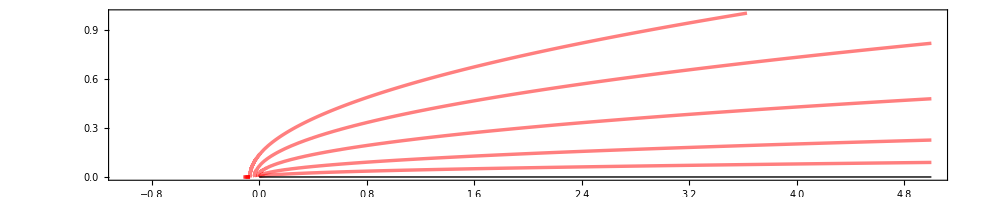

```mathematica
a=Show[
ContourPlot[Erfc[η] /. sol[[4]] /. ϵ -> 0.05 ,{x,-1,5},{y,0,1}, AspectRatio -> 1/5, Contours -> {0.1,0.25,0.5,0.75,0.9}, Exclusions->{y==0},ContourStyle -> {{Thickness[0.0025],Red}},ContourShading -> False,PlotPoints -> {30,100}],Graphics[{Thick,Line[{{0,0},{5,0}}]}]]
```

```mathematica
f =Erfc[η] /. sol[[4]]  /. ϵ -> 0.05
```

Erfc[(-56.5685 x √(0.05 x+0.05 √(x^2+y^2))+565.685 (0.05 x+0.05 √(x^2+y^2))^(3/2))/(2 y)]

```mathematica
Manipulate[
Show[
ContourPlot[Evaluate[Erfc[η] /. sol[[4]]  /. ϵ -> ϵ1],{x,-1,5},{y,0,1}, AspectRatio -> 1/5, Contours -> {0.1,0.25,0.5,0.75,0.9}, Exclusions->{y==0},ContourStyle -> {{Thickness[0.0025],Red}},ContourShading -> False,PlotPoints -> {30,100}],
Graphics[{Thick,Line[{{0,0},{5,0}}]}]]
,{ϵ1,0.05,0.1}]
```

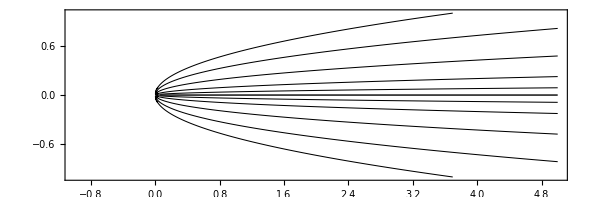

```mathematica
b=Show[
ContourPlot[Erfc[Abs[y]/(2 √(ϵ x))] /. ϵ -> 0.05 ,{x,-1,5},{y,-1,1}, AspectRatio -> 1/3, Contours -> {0.1,0.25,0.5,0.75,0.9}, Exclusions->{y==0},ContourStyle -> Thickness[0.00125],ContourShading -> False,PlotPoints -> {30,100}],Graphics[{Thick,Line[{{0,0},{5,0}}]}]]
```

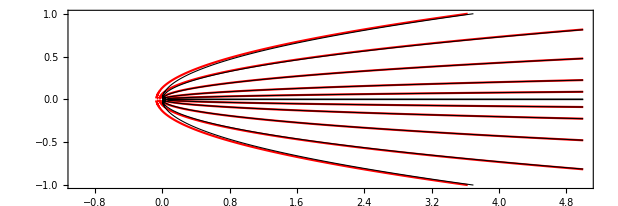

```mathematica
Show[a,b]
```

```mathematica
Manipulate[
Show[
ContourPlot[Evaluate[Erfc[η] /. sol[[4]] /. ϵ -> 10^ϵ1 ],{x,-1 L,5 L},{y,0.001,1L}, AspectRatio -> 1/5, Contours -> {0.25,0.5,0.75,0.9}, Exclusions->{y==0},ContourStyle -> {{Thickness[0.0025],Red}},ContourShading -> False,PlotPoints -> {30,100}],
ContourPlot[Evaluate[Erfc[Abs[y]/(2 √(ϵ x))] /. ϵ -> 10^ϵ1  ],{x,-1L,5L},{y,0.001,1L}, AspectRatio -> 1/5, Contours -> {0.25,0.5,0.75,0.9}, Exclusions->{y==0},ContourStyle -> Thickness[0.00125],ContourShading -> False,PlotPoints -> {100,100}],Graphics[{Thick,Line[{{0,0},{5L,0}}]}]]
,{ϵ1,-2,0},{L,1,10}]
```